```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/ignition/cantera/ratematrix

```mathematica
filebase="data/h2o2test"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime} = dat[[1,1;;3]]
elements={"O","H","Ar"};
file=OpenRead[filebase<>"ratematrix.npy","BinaryFormat"->True];
A=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
file=OpenRead[filebase<>"eigenvalues.npy","BinaryFormat"->True];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2];
Close[file];
file=OpenRead[filebase<>"eigenvectors.npy","BinaryFormat"->True];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2],dim];
Close[file];
file=OpenRead[filebase<>"spatoms.npy","BinaryFormat"->True];
spatoms=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[elements]];
Close[file];
file=OpenRead[filebase<>"multiindices.npy","BinaryFormat"->True];
multiindices=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[spatoms]];
Close[file];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,10},{65,65}}],ListPlot[{Re[#]/Max[Abs[evals]],Im[#]/Max[Abs[evals]]}&/@evals,ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Im[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],None},{DisplayForm[RowBox[{Re[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,10},{65,65}}]},{MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,10},{65,65}}],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,10},{65,65}}]}}]
Export["plots/example.pdf",p]
multiforms[[Reverse[Ordering[Abs[Eigensystem[A][[2,-1]]]]]]]
```

data/h2o2test

{35,4324,0.328147}

-Graphics-

plots/example.pdf

{5 (Ar_1)+10 (O_1 H_2),5 (Ar_1)+2 (H_2)+6 (O_1 H_2)+2 (O_2 H_2),5 (Ar_1)+3 (H_2)+4 (O_1 H_2)+3 (O_2 H_2),5 (Ar_1)+2 (H_2)+8 (O_1 H_2)+O_2,5 (Ar_1)+H_2+8 (O_1 H_2)+O_2 H_2,4315,5 (Ar_1)+12 (H_1)+2 (O_1)+4 (O_2 H_2),5 (Ar_1)+14 (H_1)+4 (O_1)+3 (O_2 H_2),5 (Ar_1)+10 (H_1)+5 (O_2 H_2),5 (Ar_1)+8 (H_1)+H_2+5 (O_2 H_2)}
 |  |  |  |

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

{{9,19,0.00157568,332,9},{12,48,0.00369882,1225,12},{15,89,0.00906399,3588,15},{18,177,0.0268147,9583,18},{21,298,0.0673564,22616,21},{24,516,0.151661,50049,24},{27,807,0.351585,102480,27},{30,1277,0.745929,200145,30},{33,1888,1.46202,370476,33},{36,2803,2.79616,661388,36},{39,3965,5.17267,1135106,39},{42,5612,9.34858,1893255,42},{45,7663,15.0369,3063616,45},{48,10450,24.728,4844184,48},{51,13862,35.2001,7477740,51},{54,18348,64.6246,11324874,54},{57,23760,139.444,16818920,57},{60,30688,328.017,24581466,60}}

{{9,19,0,83,3},{12,48,1,245,4},{15,89,1,598,5},{18,177,1,1369,6},{21,298,2,2827,7},{24,516,3,5561,8},{27,807,4,10248,9},{30,1277,4,18195,10},{33,1888,5,30873,11},{36,2803,5,50876,12},{39,3965,7,81079,13},{42,5612,8,126217,14},{45,7663,9,191476,15},{48,10450,10,284952,16},{51,13862,11,415430,17},{54,18348,12,596046,18},{57,23760,14,840946,19},{60,30688,16,1170546,20},{63,38940,17,1606694,21},{66,49274,18,2180000,22},{69,61446,20,2923048,23},{72,76411,22,3880353,24},{75,93864,24,5099087,25},{78,114989,26,6642312,26},{81,139411,29,8576593,27},{84,168576,32,10989255,28},{87,202029,34,13972160,29},{90,241515,37,17643841,30},{93,286488,40,22128615,31},{96,339030,44,27584561,32},{99,398493,47,34177030,33},{102,467337,51,42113553,34},{105,544800,56,51610691,35},{108,633763,60,62937086,36},{111,733337,65,76372469,37},{114,846870,72,92260201,38},{117,973333,79,110957124,39},{120,1116588,86,132897080,40}}

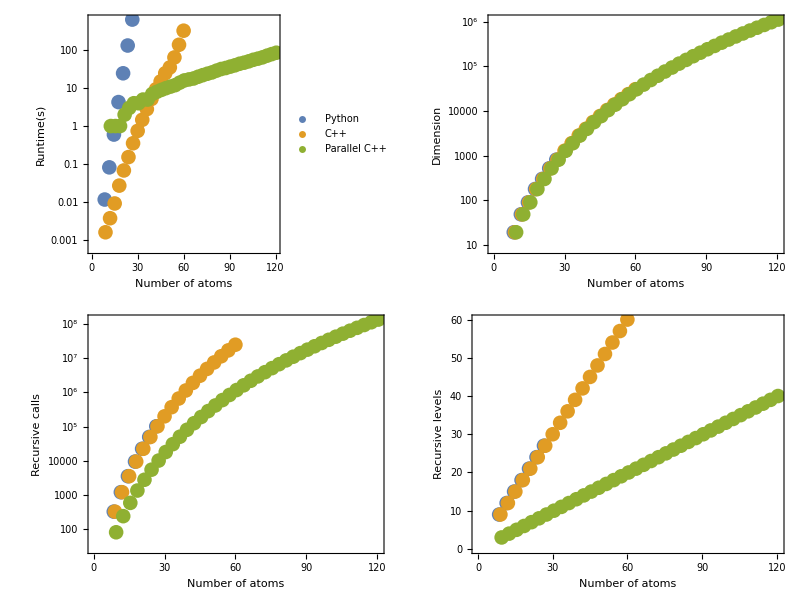

plots/runtimes.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
dat2=Import["data/runtimes2out.dat"]
dat3=Import["data/runtimes3out.dat"]
p=Legended[Grid[{{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,3}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,3}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,3}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,2}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,2}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,2}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]},{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,4}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,4}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,4}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,5}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,5}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,5}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]}}],Placed[PointLegend[ColorData[97,"ColorList"][[1;;3]],{"Python","C++","Parallel C++"},LegendMarkerSize->20],Right]]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

```mathematica
press0=0.5;
press1=10.0;
temp0=1000;
temp1=2500;
ntemp=25;
npres=25;
sweep=Import["data/sweepout.dat"];
p=Grid[{{ArrayPlot[Transpose[Partition[Log[Abs[Min[#[[4;;-2]]]]]&/@sweep[[2;;-1]],ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,-1]]},{"Pressure (atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,press0+(press1-press0)*i/npres},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[Mean[#[[4;;-2]]]]]&/@sweep[[2;;-1]],ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-OverBar[λ]]},{"Pressure (atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,press0+(press1-press0)*i/npres},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[Max[#[[4;;-2]]]]]&/@sweep[[2;;-1]],ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,1]]},{"Pressure (atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,press0+(press1-press0)*i/npres},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True]}}]
Export["plots/sweep.pdf",p]
```

-Graphics- | -Graphics- | -Graphics-

plots/sweep.pdf